# Mały projekt 4 - Metoda najmniejszych kwadratów

## Jan Czechowski

## Zadanie 1. -Graphics-

Wspolczynniki {a, b}: {4.632,0.573}

Dopasowana funkcja: 4.632+0.573 x

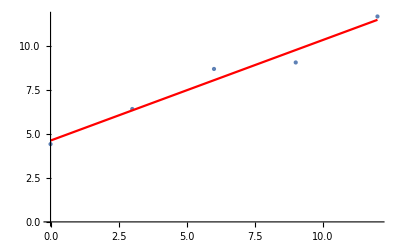

```mathematica
dane1={{0,4.43},{3,6.43},{6,8.71},{9,9.08},{12,11.7}};
macierz1=Table[{1,x[[1]]},{x,dane1}];
wektor1=dane1[[All,2]];
wynik1=LeastSquares[macierz1,wektor1];
Print["Wspolczynniki {a, b}: ",wynik1];
dopasowanie1=Fit[dane1,{1,x},x];
Print["Dopasowana funkcja: ",dopasowanie1];
wykres1=ListPlot[dane1,PlotStyle->PointSize[Large]];
linia1=Plot[dopasowanie1,{x,0,12},PlotStyle->Red];
Show[wykres1,linia1]
```

## Zadanie 2. -Graphics-

Wspolczynniki {a, b}: {289/15,-323/165}

Dopasowana funkcja: 19.2667-1.95758 x

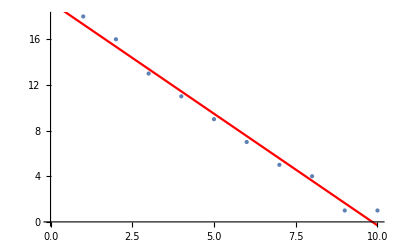

```mathematica
dane2={{1,18},{2,16},{3,13},{4,11},{5,9},{6,7},{7,5},{8,4},{9,1},{10,1}};
macierz2=Table[{1,x[[1]]},{x,dane2}];
wektor2=dane2[[All,2]];
wynik2=LeastSquares[macierz2,wektor2];
Print["Wspolczynniki {a, b}: ",wynik2];
dopasowanie2=Fit[dane2,{1,x},x];
Print["Dopasowana funkcja: ",dopasowanie2];
wykres2=ListPlot[dane2,PlotStyle->PointSize[Large]];
linia2=Plot[dopasowanie2,{x,0,10},PlotStyle->Red];
Show[wykres2,linia2]
```

## Zadanie 3. -Graphics-

Dopasowana funkcja: 3.85714+1.0119 x+0.940476 x^2

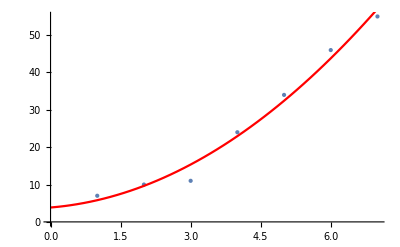

```mathematica
dane3={{1,7},{2,10},{3,11},{4,24},{5,34},{6,46},{7,55}};
dopasowanie3=Fit[dane3,{1,x,x^2},x];
Print["Dopasowana funkcja: ",dopasowanie3];
wykres3=ListPlot[dane3,PlotStyle->PointSize[Large]];
linia3=Plot[dopasowanie3,{x,0,7},PlotStyle->Red];
Show[wykres3,linia3]
```

## Zadanie 4.

Dopasowana funkcja prosta: 1.13658+0.92968 x

Dopasowana funkcja wielomianowa: 2.85013-0.668452 x+0.337605 x^2-0.0140625 x^3

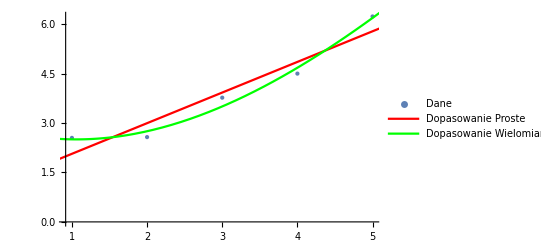

```mathematica
dane4={{1,2.54968},{2,2.57332},{3,3.77028},{4,4.50018},{5,6.23465}};
dopasowanie4Proste=Fit[dane4,{1,x},x];
Print["Dopasowana funkcja prosta: ",dopasowanie4Proste];
dopasowanie4Wielomianowe=Fit[dane4,{1,x,x^2,x^3},x];
Print["Dopasowana funkcja wielomianowa: ",dopasowanie4Wielomianowe];
wykres4=ListPlot[dane4,PlotStyle->PointSize[Large],PlotLegends->{"Dane"}];
linia4Prosta=Plot[dopasowanie4Proste,{x,0,6},PlotStyle->Red,PlotLegends->{"Dopasowanie Proste"}];
linia4Wielomianowa=Plot[dopasowanie4Wielomianowe,{x,0,6},PlotStyle->Green,PlotLegends->{"Dopasowanie Wielomianowe"}];
Show[wykres4,linia4Prosta,linia4Wielomianowa]
```